```mathematica
Data Set 1:SYS2.DAT-86 time-between-failures[14] is converted to time to failures and scaled.
```

```mathematica
4.79,7.45,10.22,15.76,26.10,28.59,35.52,41.49,42.66,44.36,45.53,58.27,62.96,74.70,81.63,100.71,102.06,104.83,110.79,118.36,122.73,145.03,149.40,152.80,156.85,162.20,164.97,168.60,173.82,179.95,182.72,195.72,203.93,206.06,222.26,238.27,241.25,249.99,256.17,282.57,282.62,284.11,294.45,318.86,323.46,329.11,340.30,344.67,353.94,398.56,405.70,407.51,422.36,429.93,461.47,482.62,491.46,511.83,526.64,532.23,537.13,543.06,560.75,561.60,589.96,592.09,610.75,615.65,630.52,673.74,687.92,698.15,753.05,768.25,801.06,828.22,849.97,885.02,892.27,911.90,951.69,962.59,965.04,
976.98,986.92,1025.94
```

```mathematica
n=86;m=40;T=300;t=0.3;q=0.05;ns=1;J=13;jj=1;nmcmc=11000;nburn=1000;a1=0;b1=0;ξ1=0;γ1=0;R={1,1,0,1,2,1,0,2,1,3,1,1,0,1,2,1,1,2,1,3,1,1,0,1,2,1,1,2,1,3,1,1,1,0,1,0,1,1,2,1};
x={4.79,7.45,10.22,15.76,26.10,28.59,35.52,41.49,42.66,45.53,58.27,62.96,81.63,100.71,104.83,110.79,118.36,122.73,145.03,149.40,152.80,156.85,162.20,164.97,182.72,195.72,203.93,238.27,249.99,282.57,340.30,344.67,407.51,429.93,673.74,687.92,801.06,828.22,885.02,951.69};
Off[FindRoot ::lstol];
Off[Power::"infy"];
l=(∏_(i=1)^m (ⅇ^((1-ⅇ^(x[[i]] δ)) β+x[[i]] δ) β δ ))*(∏_(i=1)^J (ⅇ^((1-ⅇ^(x[[i]] δ)) β))^R[[i]])*(ⅇ^((1-ⅇ^(x[[m]] δ)) β))^(n-m-∑_(i=1)^J R[[i]]);
L=Log[l];
{δM[jj],βM[jj]}={δ,β}/.FindRoot[{D[L, δ]==0,D[L, β]==0},{{δ,0.0001},{β,0.0001}}];
f11[δ_,β_]=-D[L,δ,δ];
f22[δ_,β_]=-D[L,β,β];
f21[δ_,β_]=-D[L,δ,β];
SM[jj]=ⅇ^((1-ⅇ^(t δM[jj])) βM[jj]);
HM[jj]=βM[jj]  δM[jj] ⅇ^(δM[jj] t) ;
m1=Inverse[{{f11[δM[jj],βM[jj]],f21[δM[jj],βM[jj]]},{f21[δM[jj],βM[jj]],f22[δM[jj],βM[jj]]}}];
(*Approximate  interval estimation*)
Z=Quantile[NormalDistribution[0,1],1-(q/2)];
δL[jj]=δM[jj]-Z*Sqrt[m1[[1,1]]];
δU[jj]=δM[jj]+Z*Sqrt[m1[[1,1]]];
Lenδ[jj]=δU[jj]-δL[jj];
βL[jj]=βM[jj]-Z*Sqrt[m1[[2,2]]];
βU[jj]=βM[jj]+Z*Sqrt[m1[[2,2]]];
Lenβ[jj]=βU[jj]-βL[jj];
SS=ⅇ^((1-ⅇ^(t δδ)) ββ);
HH=ββ  δδ ⅇ^(δδ t)  ;
BS11[δδ_,ββ_]=D[SS,δδ];BS12[δδ_,ββ_]=D[SS,ββ];
mS={{BS11[δM[jj],βM[jj]]},{BS12[δM[jj],βM[jj]]}};
GS=MatrixForm[mS];
G1S=Transpose[mS];
MatrixForm[G1S];
VSS=G1S.m1.mS;
VarSS=VSS[[1,1]];
BH11[δδ_,ββ_]=D[HH,δδ];BH12[δδ_,ββ_]=D[HH,ββ];
mH={{BH11[δM[jj],βM[jj]]},{BH12[δM[jj],βM[jj]]}};
GH=MatrixForm[mH];
G1H=Transpose[mH];
MatrixForm[G1H];
VHH=G1H.m1.mH;
VarHH=VHH[[1,1]];
SL[jj]=SM[jj]-Z*Sqrt[VarSS];
SU[jj]=SM[jj]+Z*Sqrt[VarSS];
LenSm[jj]=SU[jj]-SL[jj];
HL[jj]=HM[jj]-Z*Sqrt[VarHH];
HU[jj]=HM[jj]+Z*Sqrt[VarHH];
LenHm[jj]=Abs[HU[jj]-HL[jj]];
(*Bayes MCMC (δ=u,β=v*)
gg[u_,v_]:=(u^(m+a1-1))*ⅇ^(-u b1)*(∏_(i=1)^m (ⅇ^((1-ⅇ^(x[[i]] u)v) +x[[i]] u) ))*(∏_(i=1)^J (ⅇ^((1-ⅇ^(x[[i]] u)) v R[[i]])))*(ⅇ^((1-ⅇ^(x[[m]] u)) v (n-m-∑_(i=1)^J R[[i]])));
gg1[u_,v_]:=(v^(m+γ1-1))*ⅇ^(-v ξ1)*(∏_(i=1)^m (ⅇ^((1-ⅇ^(x[[i]] u)) v)  ))*(∏_(i=1)^J (ⅇ^((1-ⅇ^(x[[i]] u)) v R[[i]])))*(ⅇ^((1-ⅇ^(x[[m]] u)) v (n-m-∑_(i=1)^J R[[i]])));
δ2[0]=δM[jj];
β2[0]=βM[jj];
Do[w[δ_,β_]=δ^(β-1) ⅇ^-δ;Label[mcmc3];
δ1star=RandomReal[NormalDistribution[δ2[j-1],m1[[1,1]]^0.5]];If[Im[gg[δ1star,β2[j-1]]/gg[δ2[j-1],β2[j-1]]]≠0,Goto[mcmc3]];
rr1=Min[1,gg[δ1star,β2[j-1]]/gg[δ2[j-1],β2[j-1]]];
If[RandomReal[]≤rr1, δ2[j]=δ1star,δ2[j]=δ2[j-1]];Label[mcmc4];β1star=RandomReal[(GammaDistribution[m+γ1,1/(ξ1-∑_(i=1)^m (1-ⅇ^(δ2[j]  x[[i]]))-∑_(i=1)^J ((1-ⅇ^(δ2[j] x[[i]]))R[[i]])-(1- ⅇ^(δ2[j] x[[m]]))(n-m-∑_(i=1)^J R[[i]]))])];rr11=Min[1,(gg1[δ2[j],β1star]/gg1[δ2[j],β2[j-1]])×(w[δ2[j],β1star]/w[β1star,δ2[j]])];If[Im[(gg1[δ2[j],β1star]/gg1[δ2[j],β2[j-1]])×(w[δ2[j],β1star]/w[β1star,δ2[j]])]≠0,Goto[mcmc4]];
If[RandomReal[]≤rr11, β2[j]=β1star,β2[j]=β2[j-1]],{j,1,nmcmc}];
δ1B[jj]=(1/(nmcmc-nburn))*∑_(i=nburn+1)^nmcmc δ2[i];
β1B[jj]=(1/(nmcmc-nburn))*∑_(i=nburn+1)^nmcmc β2[i];
SS2=ⅇ^((1-ⅇ^(t δ2)) β2);
HH2=β2  δ2 ⅇ^(δ2 t) ;
SM2[jj]=ⅇ^((1-ⅇ^(t δ1B[jj])) β1B[jj]);
HM2[jj]=β1B[jj]  δ1B[jj] ⅇ^(δ1B[jj] t) ;
m12=Inverse[{{f11[δ1B[jj],β1B[jj]],f21[δ1B[jj],β1B[jj]]},{f21[δ1B[jj],β1B[jj]],f22[δ1B[jj],β1B[jj]]}}];
MatrixForm[m12];
BS211[δ2_,β2_]=D[SS2,δ2];BS212[δ2_,β2_]=D[SS2,β2];
mS2={{BS211[δ1B[jj],β1B[jj]]},{BS212[δ1B[jj],β1B[jj]]}};
GS2=MatrixForm[mS2];
G1S2=Transpose[mS2];
MatrixForm[G1S2];
VSS2=G1S2.m12.mS2;
VarSS2=VSS2[[1,1]];
BH211[δ2_,β2_]=D[HH2,δ2];BH212[δ2_,β2_]=D[HH2,β2];
mH2={{BH211[δ1B[jj],β1B[jj]]},{BH212[δ1B[jj],β1B[jj]]}};
GH2=MatrixForm[mH2];
G1H2=Transpose[mH2];
MatrixForm[G1H2];
VHH2=G1H2.m12.mH2;
VarHH2=VHH2[[1,1]];
SL2[jj]=SM2[jj]-Z*Sqrt[VarSS2];
SU2[jj]=SM2[jj]+Z*Sqrt[VarSS2];
LenSm2[jj]=SU2[jj]-SL2[jj];
HL2[jj]=HM2[jj]-Z*Sqrt[VarHH2];
HU2[jj]=HM2[jj]+Z*Sqrt[VarHH2];
LenHm2[jj]=Abs[HU2[jj]-HL2[jj]];
b1mδ=Sort[Table[δ2[i],{i,nburn+1,nmcmc}]];
a1mδ=Sort[Table[β2[i],{i,nburn+1,nmcmc}]];
L1δδ[jj]=b1mδ[[251]];
U1δδ[jj]=b1mδ[[9749]];
L1ββ[jj]=a1mδ[[251]];
U1ββ[jj]=a1mδ[[9749]];
dd111[jj]=U1δδ[jj]-L1δδ[jj];
dd122[jj]=U1ββ[jj]-L1ββ[jj];

(* MLE    *)
δL=(1/ns)*∑_(i=1)^ns δL[i];δU=(1/ns)*∑_(i=1)^ns δU[i];βL=(1/ns)*∑_(i=1)^ns βL[i];βU=(1/ns)*∑_(i=1)^ns βU[i];
SL=(1/ns)*∑_(i=1)^ns SL[i];SU=(1/ns)*∑_(i=1)^ns SU[i];
HL=(1/ns)*∑_(i=1)^ns HL[i];HU=(1/ns)*∑_(i=1)^ns HU[i];
δM1=(1/ns)*∑_(i=1)^ns δM[i];βM1=(1/ns)*∑_(i=1)^ns βM[i];
Means=Round[(1/ns)*∑_(jj=1)^ns SM[jj],0.0001];
MeanH=Round[(1/ns)*∑_(jj=1)^ns HM[jj],0.0001];
md3=Round[(1/ns)*∑_(jj=1)^ns LenSm[jj],0.0001];
md4=Round[(1/ns)*∑_(jj=1)^ns LenHm[jj],0.0001];

(* prior0  *)
δL2=(1/ns)*∑_(i=1)^ns L1δδ[i];δU2=(1/ns)*∑_(i=1)^ns U1δδ[i];βL2=(1/ns)*∑_(i=1)^ns L1ββ[i];βU2=(1/ns)*∑_(i=1)^ns U1ββ[i];
SL2=(1/ns)*∑_(i=1)^ns SL2[i];SU2=(1/ns)*∑_(i=1)^ns SU2[i];
HL2=(1/ns)*∑_(i=1)^ns HL2[i];HU2=(1/ns)*∑_(i=1)^ns HU2[i];
δB51=(1/ns)*∑_(i=1)^ns δ1B[i];BB51=(1/ns)*∑_(i=1)^ns β1B[i];

Means2=Round[(1/ns)*∑_(jj=1)^ns SM2[jj],0.0001];
MeanH2=Round[(1/ns)*∑_(jj=1)^ns HM2[jj],0.0001];

Print[Style[Grid[{{ML, point estimation,lower ,upper,length},
{δ,Round[δM1,0.0001],Round[δL,0.0001], Round[δU,0.0001],Round[δU,0.0001]-Round[δL,0.0001]},{β,Round[βM1,0.0001], Round[βL,0.0001], Round[βU,0.0001], Round[βU,0.0001]-Round[βL,0.0001]},{S,Round[Means,0.0001],Round[SL,0.0001], Round[SU,0.0001],Round[SU,0.0001]-Round[SL,0.0001]},{H,Round[MeanH,0.0001],Round[HL,0.0001], Round[HU,0.0001],Round[HU,0.0001]-Round[HL,0.0001]}}, Dividers->All, ItemSize->Automatic,Background->{{Pink},{Yellow},None}],FontSize->18]];

Print[Style[Grid[{{mcmc0,point estimation,lower ,upper,length},{δ,Round[δB51,0.0001],Round[δL2,0.0001],Round[δU2,0.0001],Round[δU2,0.0001]-Round[δL2,0.0001]},{β,Round[BB51,0.0001],Round[βL2,0.0001],Round[βU2,0.0001],Round[βU2,0.0001]-Round[βL2,0.0001]},{S,Round[Means2,0.0001],Round[SL2,0.0001],Round[SU2,0.0001],Round[SU2,0.0001]-Round[SL2,0.0001]},{H,Round[MeanH2,0.0001],Round[HL2,0.0001],Round[HU2,0.0001],Round[HU2,0.0001]-Round[HL2,0.0001]}}, Dividers->All, ItemSize->Automatic,Background->{{Pink},{Yellow},None}],FontSize->18]]
```

ML | estimation point | lower | upper | length
δ | 0.0012 | 0.0008 | 0.0017 | 0.0009
β | 0.3533 | 0.1584 | 0.5482 | 0.3898
S | 0.9999 | 0.9998 | 0.9999 | 0.0001
H | 0.0004 | 0.0003 | 0.0006 | 0.0003

mcmc0 | estimation point | lower | upper | length
δ | 0.0005 | 0.0003 | 0.0008 | 0.0005
β | 1.3814 | 0.7815 | 2.1208 | 1.3393
S | 0.9998 | 0.9997 | 0.9999 | 0.0002
H | 0.0007 | 0.0005 | 0.001 | 0.0005

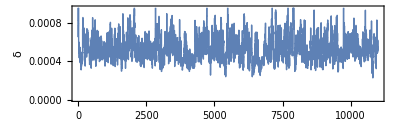

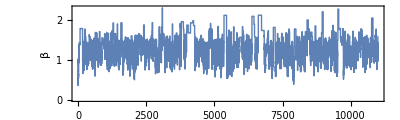

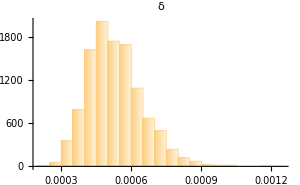

System`HistogramDump`fn$4945::chelfn: Value of option ChartElementFunction -> FadingRectangl is not a valid chart element function, or an appropriate ChartElementData entity.

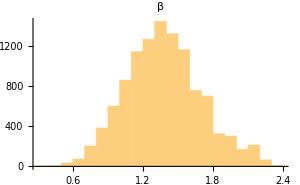

{0.000531954,1.38144}

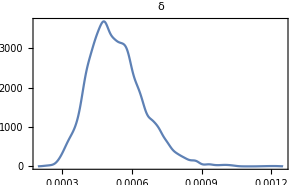

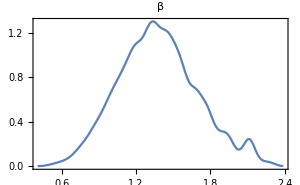

```mathematica
mcmc11=Table[δ2[i],{i,1,nmcmc}];
mcmc33=Table[β2[i],{i,1,nmcmc}];
ListLinePlot[mcmc11,Frame->True,FrameLabel->{iteration,δ},ImageSize->Scaled[.2],PlotStyle->Thick,AspectRatio->0.3,ImageSize->Medium]
ListLinePlot[mcmc33,Frame->True,FrameLabel->{iteration,β},ImageSize->Scaled[.2],PlotStyle->Thick,AspectRatio->0.3,ImageSize->Medium]
Histogram[mcmc11,Axes->{True,False},ImageSize->300,PlotLabel->"δ",PlotRange->All,ChartElementFunction->"FadingRectangle"]
Histogram[mcmc33,Axes->{True,False},ImageSize->300,PlotLabel->"β",PlotRange->All,ChartElementFunction->"FadingRectangl"]
{Mean[b1mδ],Mean[a1mδ]}
SmoothHistogram[mcmc11,Axes->{True,False},Frame->True,ImageSize->300,PlotLabel->"δ",PlotRange->All]
SmoothHistogram[mcmc33,Axes->{True,False},Frame->True,ImageSize->300,PlotLabel->"β",PlotRange->All]
```

```mathematica
Data Set 2:The following data set includes the survival times
(in days) of 72 guinea pigs infected with virulent tubercle
bacilli,observed and reported by Bjerkedal[2].
```

```mathematica
10,33,44,56,59,72,74,77,92,93,96,100,100,102,105,107,107,108,108,108,109,112,113,115,116,120,121,122,122,124,130,134,136,139,144,146,153,159,160,163,163,168,171,172,176,183,195,196,197,202,213,215,216,222,230,231,240,245,251,253,254,254,278,293,327,342,347,361,402,432,458,555
```

```mathematica
n=72;m=50;T=300;t=0.3;q=0.05;ns=1;J=13;jj=1;nmcmc=11000;nburn=1000;a1=0;b1=0;ξ1=0;γ1=0;R={1,0,0,1,0,1,0,1,1,0,2,0,0,1,1,0,2,0,0,1,2,0,0,1,1,0,0,1,1,0,0,0,0,1,0,1,0,1,1,1};
x={10,33,56,59,72,77,92,93,100,100,105,107,107,108,108,112,113,115,116,121,122,124,134,139,144,153,160,163,168,172,183,196,197,202,215,216,230,231,240,245,251,253,254,278,293,327,342,347,402,458};Off[FindRoot ::lstol];
Off[Power::"infy"];
l=(∏_(i=1)^m (ⅇ^((1-ⅇ^(x[[i]] δ)) β+x[[i]] δ) β δ ))*(∏_(i=1)^J (ⅇ^((1-ⅇ^(x[[i]] δ)) β))^R[[i]])*(ⅇ^((1-ⅇ^(x[[m]] δ)) β))^(n-m-∑_(i=1)^J R[[i]]);
L=Log[l];
{δM[jj],βM[jj]}={δ,β}/.FindRoot[{D[L, δ]==0,D[L, β]==0},{{δ,0.0001},{β,0.001}}];
f11[δ_,β_]=-D[L,δ,δ];
f22[δ_,β_]=-D[L,β,β];
f21[δ_,β_]=-D[L,δ,β];
SM[jj]=ⅇ^((1-ⅇ^(t δM[jj])) βM[jj]);
HM[jj]=βM[jj]  δM[jj] ⅇ^(δM[jj] t) ;
m1=Inverse[{{f11[δM[jj],βM[jj]],f21[δM[jj],βM[jj]]},{f21[δM[jj],βM[jj]],f22[δM[jj],βM[jj]]}}];
(*Approximate  interval estimation*)
Z=Quantile[NormalDistribution[0,1],1-(q/2)];
δL[jj]=δM[jj]-Z*Sqrt[m1[[1,1]]];
δU[jj]=δM[jj]+Z*Sqrt[m1[[1,1]]];
Lenδ[jj]=δU[jj]-δL[jj];
βL[jj]=βM[jj]-Z*Sqrt[m1[[2,2]]];
βU[jj]=βM[jj]+Z*Sqrt[m1[[2,2]]];
Lenβ[jj]=βU[jj]-βL[jj];
SS=ⅇ^((1-ⅇ^(t δδ)) ββ);
HH=ββ  δδ ⅇ^(δδ t)  ;
BS11[δδ_,ββ_]=D[SS,δδ];BS12[δδ_,ββ_]=D[SS,ββ];
mS={{BS11[δM[jj],βM[jj]]},{BS12[δM[jj],βM[jj]]}};
GS=MatrixForm[mS];
G1S=Transpose[mS];
MatrixForm[G1S];
VSS=G1S.m1.mS;
VarSS=VSS[[1,1]];
BH11[δδ_,ββ_]=D[HH,δδ];BH12[δδ_,ββ_]=D[HH,ββ];
mH={{BH11[δM[jj],βM[jj]]},{BH12[δM[jj],βM[jj]]}};
GH=MatrixForm[mH];
G1H=Transpose[mH];
MatrixForm[G1H];
VHH=G1H.m1.mH;
VarHH=VHH[[1,1]];
SL[jj]=SM[jj]-Z*Sqrt[VarSS];
SU[jj]=SM[jj]+Z*Sqrt[VarSS];
LenSm[jj]=SU[jj]-SL[jj];
HL[jj]=HM[jj]-Z*Sqrt[VarHH];
HU[jj]=HM[jj]+Z*Sqrt[VarHH];
LenHm[jj]=Abs[HU[jj]-HL[jj]];
(*Bayes MCMC (δ=u,β=v*)
gg[u_,v_]:=(u^(m+a1-1))*ⅇ^(-u b1)*(∏_(i=1)^m (ⅇ^((1-ⅇ^(x[[i]] u)v) +x[[i]] u) ))*(∏_(i=1)^J (ⅇ^((1-ⅇ^(x[[i]] u)) v R[[i]])))*(ⅇ^((1-ⅇ^(x[[m]] u)) v (n-m-∑_(i=1)^J R[[i]])));
gg1[u_,v_]:=(v^(m+γ1-1))*ⅇ^(-v ξ1)*(∏_(i=1)^m (ⅇ^((1-ⅇ^(x[[i]] u)) v)  ))*(∏_(i=1)^J (ⅇ^((1-ⅇ^(x[[i]] u)) v R[[i]])))*(ⅇ^((1-ⅇ^(x[[m]] u)) v (n-m-∑_(i=1)^J R[[i]])));
δ2[0]=δM[jj];
β2[0]=βM[jj];
Do[w[δ_,β_]=δ^(β-1) ⅇ^-δ;Label[mcmc3];
δ1star=RandomReal[NormalDistribution[δ2[j-1],m1[[1,1]]^0.5]];If[Im[gg[δ1star,β2[j-1]]/gg[δ2[j-1],β2[j-1]]]≠0,Goto[mcmc3]];
rr1=Min[1,gg[δ1star,β2[j-1]]/gg[δ2[j-1],β2[j-1]]];
If[RandomReal[]≤rr1, δ2[j]=δ1star,δ2[j]=δ2[j-1]];Label[mcmc4];β1star=RandomReal[(GammaDistribution[m+γ1,1/(ξ1-∑_(i=1)^m (1-ⅇ^(δ2[j]  x[[i]]))-∑_(i=1)^J ((1-ⅇ^(δ2[j] x[[i]]))R[[i]])-(1- ⅇ^(δ2[j] x[[m]]))(n-m-∑_(i=1)^J R[[i]]))])];rr11=Min[1,(gg1[δ2[j],β1star]/gg1[δ2[j],β2[j-1]])×(w[δ2[j],β1star]/w[β1star,δ2[j]])];If[Im[(gg1[δ2[j],β1star]/gg1[δ2[j],β2[j-1]])×(w[δ2[j],β1star]/w[β1star,δ2[j]])]≠0,Goto[mcmc4]];
If[RandomReal[]≤rr11, β2[j]=β1star,β2[j]=β2[j-1]],{j,1,nmcmc}];
δ1B[jj]=(1/(nmcmc-nburn))*∑_(i=nburn+1)^nmcmc δ2[i];
β1B[jj]=(1/(nmcmc-nburn))*∑_(i=nburn+1)^nmcmc β2[i];
SS2=ⅇ^((1-ⅇ^(t δ2)) β2);
HH2=β2  δ2 ⅇ^(δ2 t) ;
SM2[jj]=ⅇ^((1-ⅇ^(t δ1B[jj])) β1B[jj]);
HM2[jj]=β1B[jj]  δ1B[jj] ⅇ^(δ1B[jj] t) ;
m12=Inverse[{{f11[δ1B[jj],β1B[jj]],f21[δ1B[jj],β1B[jj]]},{f21[δ1B[jj],β1B[jj]],f22[δ1B[jj],β1B[jj]]}}];
MatrixForm[m12];
BS211[δ2_,β2_]=D[SS2,δ2];BS212[δ2_,β2_]=D[SS2,β2];
mS2={{BS211[δ1B[jj],β1B[jj]]},{BS212[δ1B[jj],β1B[jj]]}};
GS2=MatrixForm[mS2];
G1S2=Transpose[mS2];
MatrixForm[G1S2];
VSS2=G1S2.m12.mS2;
VarSS2=VSS2[[1,1]];
BH211[δ2_,β2_]=D[HH2,δ2];BH212[δ2_,β2_]=D[HH2,β2];
mH2={{BH211[δ1B[jj],β1B[jj]]},{BH212[δ1B[jj],β1B[jj]]}};
GH2=MatrixForm[mH2];
G1H2=Transpose[mH2];
MatrixForm[G1H2];
VHH2=G1H2.m12.mH2;
VarHH2=VHH2[[1,1]];
SL2[jj]=SM2[jj]-Z*Sqrt[VarSS2];
SU2[jj]=SM2[jj]+Z*Sqrt[VarSS2];
LenSm2[jj]=SU2[jj]-SL2[jj];
HL2[jj]=HM2[jj]-Z*Sqrt[VarHH2];
HU2[jj]=HM2[jj]+Z*Sqrt[VarHH2];
LenHm2[jj]=Abs[HU2[jj]-HL2[jj]];
b1mδ=Sort[Table[δ2[i],{i,nburn+1,nmcmc}]];
a1mδ=Sort[Table[β2[i],{i,nburn+1,nmcmc}]];
L1δδ[jj]=b1mδ[[251]];
U1δδ[jj]=b1mδ[[9749]];
L1ββ[jj]=a1mδ[[251]];
U1ββ[jj]=a1mδ[[9749]];
dd111[jj]=U1δδ[jj]-L1δδ[jj];
dd122[jj]=U1ββ[jj]-L1ββ[jj];

(* MLE    *)
δL=(1/ns)*∑_(i=1)^ns δL[i];δU=(1/ns)*∑_(i=1)^ns δU[i];βL=(1/ns)*∑_(i=1)^ns βL[i];βU=(1/ns)*∑_(i=1)^ns βU[i];
SL=(1/ns)*∑_(i=1)^ns SL[i];SU=(1/ns)*∑_(i=1)^ns SU[i];
HL=(1/ns)*∑_(i=1)^ns HL[i];HU=(1/ns)*∑_(i=1)^ns HU[i];
δM1=(1/ns)*∑_(i=1)^ns δM[i];βM1=(1/ns)*∑_(i=1)^ns βM[i];
Means=Round[(1/ns)*∑_(jj=1)^ns SM[jj],0.0001];
MeanH=Round[(1/ns)*∑_(jj=1)^ns HM[jj],0.0001];
md3=Round[(1/ns)*∑_(jj=1)^ns LenSm[jj],0.0001];
md4=Round[(1/ns)*∑_(jj=1)^ns LenHm[jj],0.0001];

(* prior0  *)
δL2=(1/ns)*∑_(i=1)^ns L1δδ[i];δU2=(1/ns)*∑_(i=1)^ns U1δδ[i];βL2=(1/ns)*∑_(i=1)^ns L1ββ[i];βU2=(1/ns)*∑_(i=1)^ns U1ββ[i];
SL2=(1/ns)*∑_(i=1)^ns SL2[i];SU2=(1/ns)*∑_(i=1)^ns SU2[i];
HL2=(1/ns)*∑_(i=1)^ns HL2[i];HU2=(1/ns)*∑_(i=1)^ns HU2[i];
δB51=(1/ns)*∑_(i=1)^ns δ1B[i];BB51=(1/ns)*∑_(i=1)^ns β1B[i];

Means2=Round[(1/ns)*∑_(jj=1)^ns SM2[jj],0.0001];
MeanH2=Round[(1/ns)*∑_(jj=1)^ns HM2[jj],0.0001];

Print[Style[Grid[{{ML, point estimation,lower ,upper,length},
{δ,Round[δM1,0.0001],Round[δL,0.0001], Round[δU,0.0001],Round[δU,0.0001]-Round[δL,0.0001]},{β,Round[βM1,0.0001], Round[βL,0.0001], Round[βU,0.0001], Round[βU,0.0001]-Round[βL,0.0001]},{S,Round[Means,0.0001],Round[SL,0.0001], Round[SU,0.0001],Round[SU,0.0001]-Round[SL,0.0001]},{H,Round[MeanH,0.0001],Round[HL,0.0001], Round[HU,0.0001],Round[HU,0.0001]-Round[HL,0.0001]}}, Dividers->All, ItemSize->Automatic,Background->{{Pink},{Yellow},None}],FontSize->18]];

Print[Style[Grid[{{mcmc0,point estimation,lower ,upper,length},{δ,Round[δB51,0.0001],Round[δL2,0.0001],Round[δU2,0.0001],Round[δU2,0.0001]-Round[δL2,0.0001]},{β,Round[BB51,0.0001],Round[βL2,0.0001],Round[βU2,0.0001],Round[βU2,0.0001]-Round[βL2,0.0001]},{S,Round[Means2,0.0001],Round[SL2,0.0001],Round[SU2,0.0001],Round[SU2,0.0001]-Round[SL2,0.0001]},{H,Round[MeanH2,0.0001],Round[HL2,0.0001],Round[HU2,0.0001],Round[HU2,0.0001]-Round[HL2,0.0001]}}, Dividers->All, ItemSize->Automatic,Background->{{Pink},{Yellow},None}],FontSize->18]]
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

ML | estimation point | lower | upper | length
δ | 0.0013 | -0.0001 | 0.0028 | 0.0029
β | 1.8553 | -0.6857 | 4.3963 | 5.082
S | 0.9993 | 0.999 | 0.9995 | 0.0005
H | 0.0025 | 0.0015 | 0.0034 | 0.0019

mcmc0 | estimation point | lower | upper | length
δ | 0.002 | 0.0012 | 0.0032 | 0.002
β | 1.1712 | 0.4952 | 1.9787 | 1.4835
S | 0.9993 | 0.9993-0.0003 ⅈ | 0.9993+0.0003 ⅈ | 0.+0.0006 ⅈ
H | 0.0023 | 0.0023-0.0009 ⅈ | 0.0023+0.0009 ⅈ | 0.+0.0018 ⅈ

```mathematica
Data Set 3:The data is obtained from Lawless[13] and it
represents the number of revolution before failure of each of
23 ball bearings in the life tests and they are as follows:
```

```mathematica
17.88,28.92,33.00,41.52,42.12,45.60,48.80,51.84,51.96,54.12,55.56,67.80,68.44,68.64,68.88,84.12,93.12,98.64,105.12,105.84,127.92,128.04,173.40
```

```mathematica
n=23;m=10;T=50;t=0.3;q=0.05;ns=1;J=6;jj=1;
nmcmc=11000;nburn=1000;a1=0;b1=0;ξ1=0;γ1=0;R={1,1,0,1,2,1,1,2,1,3};
x={17.88,28.92,33,41.52,45.6,48.8,67.8,68.64,105.84,173.4};
Off[FindRoot ::lstol];
Off[Power::"infy"];
l=(∏_(i=1)^m (ⅇ^((1-ⅇ^(x[[i]] δ)) β+x[[i]] δ) β δ ))*(∏_(i=1)^J (ⅇ^((1-ⅇ^(x[[i]] δ)) β))^R[[i]])*(ⅇ^((1-ⅇ^(x[[m]] δ)) β))^(n-m-∑_(i=1)^J R[[i]]);
L=Log[l];
{δM[jj],βM[jj]}={δ,β}/.FindRoot[{D[L, δ]==0,D[L, β]==0},{{δ,0.1},{β,0.1}}];
f11[δ_,β_]=-D[L,δ,δ];
f22[δ_,β_]=-D[L,β,β];
f21[δ_,β_]=-D[L,δ,β];
SM[jj]=ⅇ^((1-ⅇ^(t δM[jj])) βM[jj]);
HM[jj]=βM[jj]  δM[jj] ⅇ^(δM[jj] t) ;
m1=Inverse[{{f11[δM[jj],βM[jj]],f21[δM[jj],βM[jj]]},{f21[δM[jj],βM[jj]],f22[δM[jj],βM[jj]]}}];
(*Approximate  interval estimation*)
Z=Quantile[NormalDistribution[0,1],1-(q/2)];
δL[jj]=δM[jj]-Z*Sqrt[m1[[1,1]]];
δU[jj]=δM[jj]+Z*Sqrt[m1[[1,1]]];
Lenδ[jj]=δU[jj]-δL[jj];
βL[jj]=βM[jj]-Z*Sqrt[m1[[2,2]]];
βU[jj]=βM[jj]+Z*Sqrt[m1[[2,2]]];
Lenβ[jj]=βU[jj]-βL[jj];
SS=ⅇ^((1-ⅇ^(t δδ)) ββ);
HH=ββ  δδ ⅇ^(δδ t)  ;
BS11[δδ_,ββ_]=D[SS,δδ];BS12[δδ_,ββ_]=D[SS,ββ];
mS={{BS11[δM[jj],βM[jj]]},{BS12[δM[jj],βM[jj]]}};
GS=MatrixForm[mS];
G1S=Transpose[mS];
MatrixForm[G1S];
VSS=G1S.m1.mS;
VarSS=VSS[[1,1]];
BH11[δδ_,ββ_]=D[HH,δδ];BH12[δδ_,ββ_]=D[HH,ββ];
mH={{BH11[δM[jj],βM[jj]]},{BH12[δM[jj],βM[jj]]}};
GH=MatrixForm[mH];
G1H=Transpose[mH];
MatrixForm[G1H];
VHH=G1H.m1.mH;
VarHH=VHH[[1,1]];
SL[jj]=SM[jj]-Z*Sqrt[VarSS];
SU[jj]=SM[jj]+Z*Sqrt[VarSS];
LenSm[jj]=SU[jj]-SL[jj];
HL[jj]=HM[jj]-Z*Sqrt[VarHH];
HU[jj]=HM[jj]+Z*Sqrt[VarHH];
LenHm[jj]=Abs[HU[jj]-HL[jj]];
(*Bayes MCMC (δ=u,β=v*)
gg[u_,v_]:=(u^(m+a1-1))*ⅇ^(-u b1)*(∏_(i=1)^m (ⅇ^((1-ⅇ^(x[[i]] u)v) +x[[i]] u) ))*(∏_(i=1)^J (ⅇ^((1-ⅇ^(x[[i]] u)) v R[[i]])))*(ⅇ^((1-ⅇ^(x[[m]] u)) v (n-m-∑_(i=1)^J R[[i]])));
gg1[u_,v_]:=(v^(m+γ1-1))*ⅇ^(-v ξ1)*(∏_(i=1)^m (ⅇ^((1-ⅇ^(x[[i]] u)) v)  ))*(∏_(i=1)^J (ⅇ^((1-ⅇ^(x[[i]] u)) v R[[i]])))*(ⅇ^((1-ⅇ^(x[[m]] u)) v (n-m-∑_(i=1)^J R[[i]])));
δ2[0]=δM[jj];
β2[0]=βM[jj];
Do[w[δ_,β_]=δ^(β-1) ⅇ^-δ;Label[mcmc3];
δ1star=RandomReal[NormalDistribution[δ2[j-1],m1[[1,1]]^0.5]];If[Im[gg[δ1star,β2[j-1]]/gg[δ2[j-1],β2[j-1]]]≠0,Goto[mcmc3]];
rr1=Min[1,gg[δ1star,β2[j-1]]/gg[δ2[j-1],β2[j-1]]];
If[RandomReal[]≤rr1, δ2[j]=δ1star,δ2[j]=δ2[j-1]];Label[mcmc4];β1star=RandomReal[(GammaDistribution[m+γ1,1/(ξ1-∑_(i=1)^m (1-ⅇ^(δ2[j]  x[[i]]))-∑_(i=1)^J ((1-ⅇ^(δ2[j] x[[i]]))R[[i]])-(1- ⅇ^(δ2[j] x[[m]]))(n-m-∑_(i=1)^J R[[i]]))])];rr11=Min[1,(gg1[δ2[j],β1star]/gg1[δ2[j],β2[j-1]])×(w[δ2[j],β1star]/w[β1star,δ2[j]])];If[Im[(gg1[δ2[j],β1star]/gg1[δ2[j],β2[j-1]])×(w[δ2[j],β1star]/w[β1star,δ2[j]])]≠0,Goto[mcmc4]];
If[RandomReal[]≤rr11, β2[j]=β1star,β2[j]=β2[j-1]],{j,1,nmcmc}];
δ1B[jj]=(1/(nmcmc-nburn))*∑_(i=nburn+1)^nmcmc δ2[i];
β1B[jj]=(1/(nmcmc-nburn))*∑_(i=nburn+1)^nmcmc β2[i];
SS2=ⅇ^((1-ⅇ^(t δ2)) β2);
HH2=β2  δ2 ⅇ^(δ2 t) ;
SM2[jj]=ⅇ^((1-ⅇ^(t δ1B[jj])) β1B[jj]);
HM2[jj]=β1B[jj]  δ1B[jj] ⅇ^(δ1B[jj] t) ;
m12=Inverse[{{f11[δ1B[jj],β1B[jj]],f21[δ1B[jj],β1B[jj]]},{f21[δ1B[jj],β1B[jj]],f22[δ1B[jj],β1B[jj]]}}];
MatrixForm[m12];
BS211[δ2_,β2_]=D[SS2,δ2];BS212[δ2_,β2_]=D[SS2,β2];
mS2={{BS211[δ1B[jj],β1B[jj]]},{BS212[δ1B[jj],β1B[jj]]}};
GS2=MatrixForm[mS2];
G1S2=Transpose[mS2];
MatrixForm[G1S2];
VSS2=G1S2.m12.mS2;
VarSS2=VSS2[[1,1]];
BH211[δ2_,β2_]=D[HH2,δ2];BH212[δ2_,β2_]=D[HH2,β2];
mH2={{BH211[δ1B[jj],β1B[jj]]},{BH212[δ1B[jj],β1B[jj]]}};
GH2=MatrixForm[mH2];
G1H2=Transpose[mH2];
MatrixForm[G1H2];
VHH2=G1H2.m12.mH2;
VarHH2=VHH2[[1,1]];
SL2[jj]=SM2[jj]-Z*Sqrt[VarSS2];
SU2[jj]=SM2[jj]+Z*Sqrt[VarSS2];
LenSm2[jj]=SU2[jj]-SL2[jj];
HL2[jj]=HM2[jj]-Z*Sqrt[VarHH2];
HU2[jj]=HM2[jj]+Z*Sqrt[VarHH2];
LenHm2[jj]=Abs[HU2[jj]-HL2[jj]];
b1mδ=Sort[Table[δ2[i],{i,nburn+1,nmcmc}]];
a1mδ=Sort[Table[β2[i],{i,nburn+1,nmcmc}]];
L1δδ[jj]=b1mδ[[251]];
U1δδ[jj]=b1mδ[[9749]];
L1ββ[jj]=a1mδ[[251]];
U1ββ[jj]=a1mδ[[9749]];
dd111[jj]=U1δδ[jj]-L1δδ[jj];
dd122[jj]=U1ββ[jj]-L1ββ[jj];

(* MLE    *)
δL=(1/ns)*∑_(i=1)^ns δL[i];δU=(1/ns)*∑_(i=1)^ns δU[i];βL=(1/ns)*∑_(i=1)^ns βL[i];βU=(1/ns)*∑_(i=1)^ns βU[i];
SL=(1/ns)*∑_(i=1)^ns SL[i];SU=(1/ns)*∑_(i=1)^ns SU[i];
HL=(1/ns)*∑_(i=1)^ns HL[i];HU=(1/ns)*∑_(i=1)^ns HU[i];
δM1=(1/ns)*∑_(i=1)^ns δM[i];βM1=(1/ns)*∑_(i=1)^ns βM[i];
Means=Round[(1/ns)*∑_(jj=1)^ns SM[jj],0.0001];
MeanH=Round[(1/ns)*∑_(jj=1)^ns HM[jj],0.0001];
md3=Round[(1/ns)*∑_(jj=1)^ns LenSm[jj],0.0001];
md4=Round[(1/ns)*∑_(jj=1)^ns LenHm[jj],0.0001];

(* prior0  *)
δL2=(1/ns)*∑_(i=1)^ns L1δδ[i];δU2=(1/ns)*∑_(i=1)^ns U1δδ[i];βL2=(1/ns)*∑_(i=1)^ns L1ββ[i];βU2=(1/ns)*∑_(i=1)^ns U1ββ[i];
SL2=(1/ns)*∑_(i=1)^ns SL2[i];SU2=(1/ns)*∑_(i=1)^ns SU2[i];
HL2=(1/ns)*∑_(i=1)^ns HL2[i];HU2=(1/ns)*∑_(i=1)^ns HU2[i];
δB51=(1/ns)*∑_(i=1)^ns δ1B[i];BB51=(1/ns)*∑_(i=1)^ns β1B[i];

Means2=Round[(1/ns)*∑_(jj=1)^ns SM2[jj],0.0001];
MeanH2=Round[(1/ns)*∑_(jj=1)^ns HM2[jj],0.0001];

Print[Style[Grid[{{ML, point estimation,lower ,upper,length},
{δ,Round[δM1,0.0001],Round[δL,0.0001], Round[δU,0.0001],Round[δU,0.0001]-Round[δL,0.0001]},{β,Round[βM1,0.0001], Round[βL,0.0001], Round[βU,0.0001], Round[βU,0.0001]-Round[βL,0.0001]},{S,Round[Means,0.0001],Round[SL,0.0001], Round[SU,0.0001],Round[SU,0.0001]-Round[SL,0.0001]},{H,Round[MeanH,0.0001],Round[HL,0.0001], Round[HU,0.0001],Round[HU,0.0001]-Round[HL,0.0001]}}, Dividers->All, ItemSize->Automatic,Background->{{Pink},{Yellow},None}],FontSize->18]];

Print[Style[Grid[{{mcmc0,point estimation,lower ,upper,length},{δ,Round[δB51,0.0001],Round[δL2,0.0001],Round[δU2,0.0001],Round[δU2,0.0001]-Round[δL2,0.0001]},{β,Round[BB51,0.0001],Round[βL2,0.0001],Round[βU2,0.0001],Round[βU2,0.0001]-Round[βL2,0.0001]},{S,Round[Means2,0.0001],Round[SL2,0.0001],Round[SU2,0.0001],Round[SU2,0.0001]-Round[SL2,0.0001]},{H,Round[MeanH2,0.0001],Round[HL2,0.0001],Round[HU2,0.0001],Round[HU2,0.0001]-Round[HL2,0.0001]}}, Dividers->All, ItemSize->Automatic,Background->{{Pink},{Yellow},None}],FontSize->18]]
```

ML | estimation point | lower | upper | length
δ | 0.0051 | -0.001 | 0.0111 | 0.0121
β | 0.604 | -0.4117 | 1.6197 | 2.0314
S | 0.9991 | 0.9984 | 0.9997 | 0.0013
H | 0.0031 | 0.0009 | 0.0053 | 0.0044

mcmc0 | estimation point | lower | upper | length
δ | 0.0047 | 0.0017 | 0.0113 | 0.0096
β | 0.8215 | 0.1396 | 1.754 | 1.6144
S | 0.9988 | 0.9986 | 0.9991 | 0.0005
H | 0.0039 | 0.003 | 0.0048 | 0.0018

```mathematica
Data Set 5:Aarset MV.How to identify bathtub hazard rate.IEEE Trans Reliability 1987;R-36(1):106-108. (Failure time of 50 items[1].
```

```mathematica
0.1,0.2,1.0,1.0,1.0,1.0,1.0,2.0,3.0,6.0,7.0,11.0,12.0,18.0,18.0,18.0,18.0,18.0,21.0,32.0,36.0,40.0,45.0,45.0,47.0,50.0,55.0,60.0,63.0,63.0,67.0,67.0,67.0,67.0,72.0,75.0,79.0,82.0,82.0,83.0,84.0,84.0,84.0,85.0,85.0,85.0,85.0,85.0,86.0,86.0
```

```mathematica
n=50;m=20;T=50;t=0.3;q=0.05;ns=1;J=6;jj=1;
nmcmc=11000;nburn=1000;a1=0;b1=0;ξ1=0;γ1=0;R={1,1,0,1,2,3,1,2,1,3,1,2,1,1,2,1,1,2,1,3};
x={0.1,0.2,1.0,1.0,6.0,7.0,12.0,18.0,18.0,18.0,36.0,
45.0,67.0,79.0,82.0,83.0,85.0,85.0,85.0,86.0};
Off[FindRoot ::lstol];
Off[Power::"infy"];
l=(∏_(i=1)^m (ⅇ^((1-ⅇ^(x[[i]] δ)) β+x[[i]] δ) β δ ))*(∏_(i=1)^J (ⅇ^((1-ⅇ^(x[[i]] δ)) β))^R[[i]])*(ⅇ^((1-ⅇ^(x[[m]] δ)) β))^(n-m-∑_(i=1)^J R[[i]]);
L=Log[l];
{δM[jj],βM[jj]}={δ,β}/.FindRoot[{D[L, δ]==0,D[L, β]==0},{{δ,0.0001},{β,0.001}}];
f11[δ_,β_]=-D[L,δ,δ];
f22[δ_,β_]=-D[L,β,β];
f21[δ_,β_]=-D[L,δ,β];
SM[jj]=ⅇ^((1-ⅇ^(t δM[jj])) βM[jj]);
HM[jj]=βM[jj]  δM[jj] ⅇ^(δM[jj] t) ;
m1=Inverse[{{f11[δM[jj],βM[jj]],f21[δM[jj],βM[jj]]},{f21[δM[jj],βM[jj]],f22[δM[jj],βM[jj]]}}];
(*Approximate  interval estimation*)
Z=Quantile[NormalDistribution[0,1],1-(q/2)];
δL[jj]=δM[jj]-Z*Sqrt[m1[[1,1]]];
δU[jj]=δM[jj]+Z*Sqrt[m1[[1,1]]];
Lenδ[jj]=δU[jj]-δL[jj];
βL[jj]=βM[jj]-Z*Sqrt[m1[[2,2]]];
βU[jj]=βM[jj]+Z*Sqrt[m1[[2,2]]];
Lenβ[jj]=βU[jj]-βL[jj];
SS=ⅇ^((1-ⅇ^(t δδ)) ββ);
HH=ββ  δδ ⅇ^(δδ t)  ;
BS11[δδ_,ββ_]=D[SS,δδ];BS12[δδ_,ββ_]=D[SS,ββ];
mS={{BS11[δM[jj],βM[jj]]},{BS12[δM[jj],βM[jj]]}};
GS=MatrixForm[mS];
G1S=Transpose[mS];
MatrixForm[G1S];
VSS=G1S.m1.mS;
VarSS=VSS[[1,1]];
BH11[δδ_,ββ_]=D[HH,δδ];BH12[δδ_,ββ_]=D[HH,ββ];
mH={{BH11[δM[jj],βM[jj]]},{BH12[δM[jj],βM[jj]]}};
GH=MatrixForm[mH];
G1H=Transpose[mH];
MatrixForm[G1H];
VHH=G1H.m1.mH;
VarHH=VHH[[1,1]];
SL[jj]=SM[jj]-Z*Sqrt[VarSS];
SU[jj]=SM[jj]+Z*Sqrt[VarSS];
LenSm[jj]=SU[jj]-SL[jj];
HL[jj]=HM[jj]-Z*Sqrt[VarHH];
HU[jj]=HM[jj]+Z*Sqrt[VarHH];
LenHm[jj]=Abs[HU[jj]-HL[jj]];
(*Bayes MCMC (δ=u,β=v*)
gg[u_,v_]:=(u^(m+a1-1))*ⅇ^(-u b1)*(∏_(i=1)^m (ⅇ^((1-ⅇ^(x[[i]] u)v) +x[[i]] u) ))*(∏_(i=1)^J (ⅇ^((1-ⅇ^(x[[i]] u)) v R[[i]])))*(ⅇ^((1-ⅇ^(x[[m]] u)) v (n-m-∑_(i=1)^J R[[i]])));
gg1[u_,v_]:=(v^(m+γ1-1))*ⅇ^(-v ξ1)*(∏_(i=1)^m (ⅇ^((1-ⅇ^(x[[i]] u)) v)  ))*(∏_(i=1)^J (ⅇ^((1-ⅇ^(x[[i]] u)) v R[[i]])))*(ⅇ^((1-ⅇ^(x[[m]] u)) v (n-m-∑_(i=1)^J R[[i]])));
δ2[0]=δM[jj];
β2[0]=βM[jj];
Do[w[δ_,β_]=δ^(β-1) ⅇ^-δ;Label[mcmc3];
δ1star=RandomReal[NormalDistribution[δ2[j-1],m1[[1,1]]^0.5]];If[Im[gg[δ1star,β2[j-1]]/gg[δ2[j-1],β2[j-1]]]≠0,Goto[mcmc3]];
rr1=Min[1,gg[δ1star,β2[j-1]]/gg[δ2[j-1],β2[j-1]]];
If[RandomReal[]≤rr1, δ2[j]=δ1star,δ2[j]=δ2[j-1]];Label[mcmc4];β1star=RandomReal[(GammaDistribution[m+γ1,1/(ξ1-∑_(i=1)^m (1-ⅇ^(δ2[j]  x[[i]]))-∑_(i=1)^J ((1-ⅇ^(δ2[j] x[[i]]))R[[i]])-(1- ⅇ^(δ2[j] x[[m]]))(n-m-∑_(i=1)^J R[[i]]))])];rr11=Min[1,(gg1[δ2[j],β1star]/gg1[δ2[j],β2[j-1]])×(w[δ2[j],β1star]/w[β1star,δ2[j]])];If[Im[(gg1[δ2[j],β1star]/gg1[δ2[j],β2[j-1]])×(w[δ2[j],β1star]/w[β1star,δ2[j]])]≠0,Goto[mcmc4]];
If[RandomReal[]≤rr11, β2[j]=β1star,β2[j]=β2[j-1]],{j,1,nmcmc}];
δ1B[jj]=(1/(nmcmc-nburn))*∑_(i=nburn+1)^nmcmc δ2[i];
β1B[jj]=(1/(nmcmc-nburn))*∑_(i=nburn+1)^nmcmc β2[i];
SS2=ⅇ^((1-ⅇ^(t δ2)) β2);
HH2=β2  δ2 ⅇ^(δ2 t) ;
SM2[jj]=ⅇ^((1-ⅇ^(t δ1B[jj])) β1B[jj]);
HM2[jj]=β1B[jj]  δ1B[jj] ⅇ^(δ1B[jj] t) ;
m12=Inverse[{{f11[δ1B[jj],β1B[jj]],f21[δ1B[jj],β1B[jj]]},{f21[δ1B[jj],β1B[jj]],f22[δ1B[jj],β1B[jj]]}}];
MatrixForm[m12];
BS211[δ2_,β2_]=D[SS2,δ2];BS212[δ2_,β2_]=D[SS2,β2];
mS2={{BS211[δ1B[jj],β1B[jj]]},{BS212[δ1B[jj],β1B[jj]]}};
GS2=MatrixForm[mS2];
G1S2=Transpose[mS2];
MatrixForm[G1S2];
VSS2=G1S2.m12.mS2;
VarSS2=VSS2[[1,1]];
BH211[δ2_,β2_]=D[HH2,δ2];BH212[δ2_,β2_]=D[HH2,β2];
mH2={{BH211[δ1B[jj],β1B[jj]]},{BH212[δ1B[jj],β1B[jj]]}};
GH2=MatrixForm[mH2];
G1H2=Transpose[mH2];
MatrixForm[G1H2];
VHH2=G1H2.m12.mH2;
VarHH2=VHH2[[1,1]];
SL2[jj]=SM2[jj]-Z*Sqrt[VarSS2];
SU2[jj]=SM2[jj]+Z*Sqrt[VarSS2];
LenSm2[jj]=SU2[jj]-SL2[jj];
HL2[jj]=HM2[jj]-Z*Sqrt[VarHH2];
HU2[jj]=HM2[jj]+Z*Sqrt[VarHH2];
LenHm2[jj]=Abs[HU2[jj]-HL2[jj]];
b1mδ=Sort[Table[δ2[i],{i,nburn+1,nmcmc}]];
a1mδ=Sort[Table[β2[i],{i,nburn+1,nmcmc}]];
L1δδ[jj]=b1mδ[[251]];
U1δδ[jj]=b1mδ[[9749]];
L1ββ[jj]=a1mδ[[251]];
U1ββ[jj]=a1mδ[[9749]];
dd111[jj]=U1δδ[jj]-L1δδ[jj];
dd122[jj]=U1ββ[jj]-L1ββ[jj];

(* MLE    *)
δL=(1/ns)*∑_(i=1)^ns δL[i];δU=(1/ns)*∑_(i=1)^ns δU[i];βL=(1/ns)*∑_(i=1)^ns βL[i];βU=(1/ns)*∑_(i=1)^ns βU[i];
SL=(1/ns)*∑_(i=1)^ns SL[i];SU=(1/ns)*∑_(i=1)^ns SU[i];
HL=(1/ns)*∑_(i=1)^ns HL[i];HU=(1/ns)*∑_(i=1)^ns HU[i];
δM1=(1/ns)*∑_(i=1)^ns δM[i];βM1=(1/ns)*∑_(i=1)^ns βM[i];
Means=Round[(1/ns)*∑_(jj=1)^ns SM[jj],0.0001];
MeanH=Round[(1/ns)*∑_(jj=1)^ns HM[jj],0.0001];
md3=Round[(1/ns)*∑_(jj=1)^ns LenSm[jj],0.0001];
md4=Round[(1/ns)*∑_(jj=1)^ns LenHm[jj],0.0001];

(* prior0  *)
δL2=(1/ns)*∑_(i=1)^ns L1δδ[i];δU2=(1/ns)*∑_(i=1)^ns U1δδ[i];βL2=(1/ns)*∑_(i=1)^ns L1ββ[i];βU2=(1/ns)*∑_(i=1)^ns U1ββ[i];
SL2=(1/ns)*∑_(i=1)^ns SL2[i];SU2=(1/ns)*∑_(i=1)^ns SU2[i];
HL2=(1/ns)*∑_(i=1)^ns HL2[i];HU2=(1/ns)*∑_(i=1)^ns HU2[i];
δB51=(1/ns)*∑_(i=1)^ns δ1B[i];BB51=(1/ns)*∑_(i=1)^ns β1B[i];

Means2=Round[(1/ns)*∑_(jj=1)^ns SM2[jj],0.0001];
MeanH2=Round[(1/ns)*∑_(jj=1)^ns HM2[jj],0.0001];

Print[Style[Grid[{{ML, point estimation,lower ,upper,length},
{δ,Round[δM1,0.0001],Round[δL,0.0001], Round[δU,0.0001],Round[δU,0.0001]-Round[δL,0.0001]},{β,Round[βM1,0.0001], Round[βL,0.0001], Round[βU,0.0001], Round[βU,0.0001]-Round[βL,0.0001]},{S,Round[Means,0.0001],Round[SL,0.0001], Round[SU,0.0001],Round[SU,0.0001]-Round[SL,0.0001]},{H,Round[MeanH,0.0001],Round[HL,0.0001], Round[HU,0.0001],Round[HU,0.0001]-Round[HL,0.0001]}}, Dividers->All, ItemSize->Automatic,Background->{{Pink},{Yellow},None}],FontSize->18]];

Print[Style[Grid[{{mcmc0,point estimation,lower ,upper,length},{δ,Round[δB51,0.0001],Round[δL2,0.0001],Round[δU2,0.0001],Round[δU2,0.0001]-Round[δL2,0.0001]},{β,Round[BB51,0.0001],Round[βL2,0.0001],Round[βU2,0.0001],Round[βU2,0.0001]-Round[βL2,0.0001]},{S,Round[Means2,0.0001],Round[SL2,0.0001],Round[SU2,0.0001],Round[SU2,0.0001]-Round[SL2,0.0001]},{H,Round[MeanH2,0.0001],Round[HL2,0.0001],Round[HU2,0.0001],Round[HU2,0.0001]-Round[HL2,0.0001]}}, Dividers->All, ItemSize->Automatic,Background->{{Pink},{Yellow},None}],FontSize->18]]
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

ML | estimation point | lower | upper | length
δ | 0.0099 | -0.0003 | 0.0201 | 0.0204
β | 0.4582 | -0.2312 | 1.1477 | 1.3789
S | 0.9986 | 0.9978 | 0.9995 | 0.0017
H | 0.0046 | 0.0018 | 0.0073 | 0.0055

mcmc0 | estimation point | lower | upper | length
δ | 0.0082 | 0.003 | 0.0191 | 0.0161
β | 0.7921 | 0.145 | 1.7734 | 1.6284
S | 0.998 | 0.9975 | 0.9986 | 0.0011
H | 0.0065 | 0.0048 | 0.0082 | 0.0034

```mathematica
Data Set 6:The data is obtained from Lai et al.[12];
Complete Data:Failure times of 20 components.
```

```mathematica
0.481,1.196,1.438,1.797,1.811,1.831,1.885,2.104,2.133,2.144,2.282,2.322,2.334,2.341,2.428,2.447,2.511,2.593,2.715,3.218
```

```mathematica
n=20;m=10;T=50;t=0.3;q=0.05;ns=1;J=6;jj=1;
nmcmc=11000;nburn=1000;a1=0;b1=0;ξ1=0;γ1=0;R={1,1,0,1,2,1,1,1,1,1};
x={0.481,1.196,1.797,1.885,2.104,2.322,2.334,2.447,2.511,2.593};
Off[FindRoot ::lstol];
Off[Power::"infy"];
l=(∏_(i=1)^m (ⅇ^((1-ⅇ^(x[[i]] δ)) β+x[[i]] δ) β δ ))*(∏_(i=1)^J (ⅇ^((1-ⅇ^(x[[i]] δ)) β))^R[[i]])*(ⅇ^((1-ⅇ^(x[[m]] δ)) β))^(n-m-∑_(i=1)^J R[[i]]);
L=Log[l];
{δM[jj],βM[jj]}={δ,β}/.FindRoot[{D[L, δ]==0,D[L, β]==0},{{δ,0.0001},{β,0.001}}];
f11[δ_,β_]=-D[L,δ,δ];
f22[δ_,β_]=-D[L,β,β];
f21[δ_,β_]=-D[L,δ,β];
SM[jj]=ⅇ^((1-ⅇ^(t δM[jj])) βM[jj]);
HM[jj]=βM[jj]  δM[jj] ⅇ^(δM[jj] t) ;
m1=Inverse[{{f11[δM[jj],βM[jj]],f21[δM[jj],βM[jj]]},{f21[δM[jj],βM[jj]],f22[δM[jj],βM[jj]]}}];
(*Approximate  interval estimation*)
Z=Quantile[NormalDistribution[0,1],1-(q/2)];
δL[jj]=δM[jj]-Z*Sqrt[m1[[1,1]]];
δU[jj]=δM[jj]+Z*Sqrt[m1[[1,1]]];
Lenδ[jj]=δU[jj]-δL[jj];
βL[jj]=βM[jj]-Z*Sqrt[m1[[2,2]]];
βU[jj]=βM[jj]+Z*Sqrt[m1[[2,2]]];
Lenβ[jj]=βU[jj]-βL[jj];
SS=ⅇ^((1-ⅇ^(t δδ)) ββ);
HH=ββ  δδ ⅇ^(δδ t)  ;
BS11[δδ_,ββ_]=D[SS,δδ];BS12[δδ_,ββ_]=D[SS,ββ];
mS={{BS11[δM[jj],βM[jj]]},{BS12[δM[jj],βM[jj]]}};
GS=MatrixForm[mS];
G1S=Transpose[mS];
MatrixForm[G1S];
VSS=G1S.m1.mS;
VarSS=VSS[[1,1]];
BH11[δδ_,ββ_]=D[HH,δδ];BH12[δδ_,ββ_]=D[HH,ββ];
mH={{BH11[δM[jj],βM[jj]]},{BH12[δM[jj],βM[jj]]}};
GH=MatrixForm[mH];
G1H=Transpose[mH];
MatrixForm[G1H];
VHH=G1H.m1.mH;
VarHH=VHH[[1,1]];
SL[jj]=SM[jj]-Z*Sqrt[VarSS];
SU[jj]=SM[jj]+Z*Sqrt[VarSS];
LenSm[jj]=SU[jj]-SL[jj];
HL[jj]=HM[jj]-Z*Sqrt[VarHH];
HU[jj]=HM[jj]+Z*Sqrt[VarHH];
LenHm[jj]=Abs[HU[jj]-HL[jj]];
(*Bayes MCMC (δ=u,β=v*)
gg[u_,v_]:=(u^(m+a1-1))*ⅇ^(-u b1)*(∏_(i=1)^m (ⅇ^((1-ⅇ^(x[[i]] u)v) +x[[i]] u) ))*(∏_(i=1)^J (ⅇ^((1-ⅇ^(x[[i]] u)) v R[[i]])))*(ⅇ^((1-ⅇ^(x[[m]] u)) v (n-m-∑_(i=1)^J R[[i]])));
gg1[u_,v_]:=(v^(m+γ1-1))*ⅇ^(-v ξ1)*(∏_(i=1)^m (ⅇ^((1-ⅇ^(x[[i]] u)) v)  ))*(∏_(i=1)^J (ⅇ^((1-ⅇ^(x[[i]] u)) v R[[i]])))*(ⅇ^((1-ⅇ^(x[[m]] u)) v (n-m-∑_(i=1)^J R[[i]])));
δ2[0]=δM[jj];
β2[0]=βM[jj];
Do[w[δ_,β_]=δ^(β-1) ⅇ^-δ;Label[mcmc3];
δ1star=RandomReal[NormalDistribution[δ2[j-1],m1[[1,1]]^0.5]];If[Im[gg[δ1star,β2[j-1]]/gg[δ2[j-1],β2[j-1]]]≠0,Goto[mcmc3]];
rr1=Min[1,gg[δ1star,β2[j-1]]/gg[δ2[j-1],β2[j-1]]];
If[RandomReal[]≤rr1, δ2[j]=δ1star,δ2[j]=δ2[j-1]];Label[mcmc4];β1star=RandomReal[(GammaDistribution[m+γ1,1/(ξ1-∑_(i=1)^m (1-ⅇ^(δ2[j]  x[[i]]))-∑_(i=1)^J ((1-ⅇ^(δ2[j] x[[i]]))R[[i]])-(1- ⅇ^(δ2[j] x[[m]]))(n-m-∑_(i=1)^J R[[i]]))])];rr11=Min[1,(gg1[δ2[j],β1star]/gg1[δ2[j],β2[j-1]])×(w[δ2[j],β1star]/w[β1star,δ2[j]])];If[Im[(gg1[δ2[j],β1star]/gg1[δ2[j],β2[j-1]])×(w[δ2[j],β1star]/w[β1star,δ2[j]])]≠0,Goto[mcmc4]];
If[RandomReal[]≤rr11, β2[j]=β1star,β2[j]=β2[j-1]],{j,1,nmcmc}];
δ1B[jj]=(1/(nmcmc-nburn))*∑_(i=nburn+1)^nmcmc δ2[i];
β1B[jj]=(1/(nmcmc-nburn))*∑_(i=nburn+1)^nmcmc β2[i];
SS2=ⅇ^((1-ⅇ^(t δ2)) β2);
HH2=β2  δ2 ⅇ^(δ2 t) ;
SM2[jj]=ⅇ^((1-ⅇ^(t δ1B[jj])) β1B[jj]);
HM2[jj]=β1B[jj]  δ1B[jj] ⅇ^(δ1B[jj] t) ;
m12=Inverse[{{f11[δ1B[jj],β1B[jj]],f21[δ1B[jj],β1B[jj]]},{f21[δ1B[jj],β1B[jj]],f22[δ1B[jj],β1B[jj]]}}];
MatrixForm[m12];
BS211[δ2_,β2_]=D[SS2,δ2];BS212[δ2_,β2_]=D[SS2,β2];
mS2={{BS211[δ1B[jj],β1B[jj]]},{BS212[δ1B[jj],β1B[jj]]}};
GS2=MatrixForm[mS2];
G1S2=Transpose[mS2];
MatrixForm[G1S2];
VSS2=G1S2.m12.mS2;
VarSS2=VSS2[[1,1]];
BH211[δ2_,β2_]=D[HH2,δ2];BH212[δ2_,β2_]=D[HH2,β2];
mH2={{BH211[δ1B[jj],β1B[jj]]},{BH212[δ1B[jj],β1B[jj]]}};
GH2=MatrixForm[mH2];
G1H2=Transpose[mH2];
MatrixForm[G1H2];
VHH2=G1H2.m12.mH2;
VarHH2=VHH2[[1,1]];
SL2[jj]=SM2[jj]-Z*Sqrt[VarSS2];
SU2[jj]=SM2[jj]+Z*Sqrt[VarSS2];
LenSm2[jj]=SU2[jj]-SL2[jj];
HL2[jj]=HM2[jj]-Z*Sqrt[VarHH2];
HU2[jj]=HM2[jj]+Z*Sqrt[VarHH2];
LenHm2[jj]=Abs[HU2[jj]-HL2[jj]];
b1mδ=Sort[Table[δ2[i],{i,nburn+1,nmcmc}]];
a1mδ=Sort[Table[β2[i],{i,nburn+1,nmcmc}]];
L1δδ[jj]=b1mδ[[251]];
U1δδ[jj]=b1mδ[[9749]];
L1ββ[jj]=a1mδ[[251]];
U1ββ[jj]=a1mδ[[9749]];
dd111[jj]=U1δδ[jj]-L1δδ[jj];
dd122[jj]=U1ββ[jj]-L1ββ[jj];

(* MLE    *)
δL=(1/ns)*∑_(i=1)^ns δL[i];δU=(1/ns)*∑_(i=1)^ns δU[i];βL=(1/ns)*∑_(i=1)^ns βL[i];βU=(1/ns)*∑_(i=1)^ns βU[i];
SL=(1/ns)*∑_(i=1)^ns SL[i];SU=(1/ns)*∑_(i=1)^ns SU[i];
HL=(1/ns)*∑_(i=1)^ns HL[i];HU=(1/ns)*∑_(i=1)^ns HU[i];
δM1=(1/ns)*∑_(i=1)^ns δM[i];βM1=(1/ns)*∑_(i=1)^ns βM[i];
Means=Round[(1/ns)*∑_(jj=1)^ns SM[jj],0.0001];
MeanH=Round[(1/ns)*∑_(jj=1)^ns HM[jj],0.0001];
md3=Round[(1/ns)*∑_(jj=1)^ns LenSm[jj],0.0001];
md4=Round[(1/ns)*∑_(jj=1)^ns LenHm[jj],0.0001];

(* prior0  *)
δL2=(1/ns)*∑_(i=1)^ns L1δδ[i];δU2=(1/ns)*∑_(i=1)^ns U1δδ[i];βL2=(1/ns)*∑_(i=1)^ns L1ββ[i];βU2=(1/ns)*∑_(i=1)^ns U1ββ[i];
SL2=(1/ns)*∑_(i=1)^ns SL2[i];SU2=(1/ns)*∑_(i=1)^ns SU2[i];
HL2=(1/ns)*∑_(i=1)^ns HL2[i];HU2=(1/ns)*∑_(i=1)^ns HU2[i];
δB51=(1/ns)*∑_(i=1)^ns δ1B[i];BB51=(1/ns)*∑_(i=1)^ns β1B[i];

Means2=Round[(1/ns)*∑_(jj=1)^ns SM2[jj],0.0001];
MeanH2=Round[(1/ns)*∑_(jj=1)^ns HM2[jj],0.0001];

Print[Style[Grid[{{ML, point estimation,lower ,upper,length},
{δ,Round[δM1,0.0001],Round[δL,0.0001], Round[δU,0.0001],Round[δU,0.0001]-Round[δL,0.0001]},{β,Round[βM1,0.0001], Round[βL,0.0001], Round[βU,0.0001], Round[βU,0.0001]-Round[βL,0.0001]},{S,Round[Means,0.0001],Round[SL,0.0001], Round[SU,0.0001],Round[SU,0.0001]-Round[SL,0.0001]},{H,Round[MeanH,0.0001],Round[HL,0.0001], Round[HU,0.0001],Round[HU,0.0001]-Round[HL,0.0001]}}, Dividers->All, ItemSize->Automatic,Background->{{Pink},{Yellow},None}],FontSize->18]];

Print[Style[Grid[{{mcmc0,point estimation,lower ,upper,length},{δ,Round[δB51,0.0001],Round[δL2,0.0001],Round[δU2,0.0001],Round[δU2,0.0001]-Round[δL2,0.0001]},{β,Round[BB51,0.0001],Round[βL2,0.0001],Round[βU2,0.0001],Round[βU2,0.0001]-Round[βL2,0.0001]},{S,Round[Means2,0.0001],Round[SL2,0.0001],Round[SU2,0.0001],Round[SU2,0.0001]-Round[SL2,0.0001]},{H,Round[MeanH2,0.0001],Round[HL2,0.0001],Round[HU2,0.0001],Round[HU2,0.0001]-Round[HL2,0.0001]}}, Dividers->All, ItemSize->Automatic,Background->{{Pink},{Yellow},None}],FontSize->18]]
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

ML | estimation point | lower | upper | length
δ | 1.5482 | 0.5489 | 2.5475 | 1.9986
β | 0.0163 | -0.0245 | 0.0571 | 0.0816
S | 0.9904 | 0.9739 | 1.0069 | 0.033
H | 0.0402 | -0.0242 | 0.1046 | 0.1288

mcmc0 | estimation point | lower | upper | length
δ | 2.1383 | 1.0135 | 3.5743 | 2.5608
β | 0.0103 | 0.0001 | 0.0581 | 0.058
S | 0.9907 | 0.9907-0.0032 ⅈ | 0.9907+0.0032 ⅈ | 0.+0.0064 ⅈ
H | 0.042 | 0.042-0.0133 ⅈ | 0.042+0.0133 ⅈ | 0.+0.0266 ⅈ